```mathematica
LaunchKernels[16]
```

{Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16)}

```mathematica
β[ω_,δ_,t_,ϵ_]:=(ω+ⅈ*δ-ϵ)IdentityMatrix[1]
```

```mathematica
T2[t_]:=T2[t]= t*IdentityMatrix[1]
```

```mathematica
T1[t_]:=T1[t]=t*IdentityMatrix[1]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,n_]:=LEFT[ω,δ,t,ϵ,n]=Module[{},J=Inverse[β[ω,δ,1,0]];B=Inverse[β[ω,δ,1,0]];T=T1[1];Do[J=Inverse[IdentityMatrix[1]-B.T.J.T].B,n];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ,7000].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ,7000].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[1]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]]
```

```mathematica
pris=Monitor[Table[{ω,tr[ω,0.01,1,0]},{ω,Range[-2,2,0.01]}],ω]
```

{{-2.,0.49875},{-1.99,0.852666},{-1.98,0.94665},{-1.97,0.973942},{-1.96,0.984763},{-1.95,0.990041},{-1.94,0.992987},{-1.93,0.994793},{-1.92,0.995979},{-1.91,0.996799},{-1.9,0.997389},{-1.89,0.997829},{-1.88,0.998164},{-1.87,0.998426},{-1.86,0.998635},{-1.85,0.998805},{-1.84,0.998943},{-1.83,0.999059},{-1.82,0.999156},{-1.81,0.999238},{-1.8,0.999309},{-1.79,0.99937},{-1.78,0.999422},{-1.77,0.999469},{-1.76,0.999509},{-1.75,0.999545},{-1.74,0.999577},{-1.73,0.999606},{-1.72,0.999632},{-1.71,0.999655},{-1.7,0.999676},{-1.69,0.999695},{-1.68,0.999712},{-1.67,0.999727},{-1.66,0.999742},{-1.65,0.999755},{-1.64,0.999767},{-1.63,0.999778},{-1.62,0.999789},{-1.61,0.999798},{-1.6,0.999807},{-1.59,0.999815},{-1.58,0.999823},{-1.57,0.99983},{-1.56,0.999837},{-1.55,0.999843},{-1.54,0.999849},{-1.53,0.999855},{-1.52,0.99986},{-1.51,0.999865},{-1.5,0.999869},{-1.49,0.999874},{-1.48,0.999878},{-1.47,0.999882},{-1.46,0.999885},{-1.45,0.999889},{-1.44,0.999892},{-1.43,0.999895},{-1.42,0.999898},{-1.41,0.999901},{-1.4,0.999904},{-1.39,0.999906},{-1.38,0.999909},{-1.37,0.999911},{-1.36,0.999914},{-1.35,0.999916},{-1.34,0.999918},{-1.33,0.99992},{-1.32,0.999922},{-1.31,0.999923},{-1.3,0.999925},{-1.29,0.999927},{-1.28,0.999928},{-1.27,0.99993},{-1.26,0.999931},{-1.25,0.999933},{-1.24,0.999934},{-1.23,0.999935},{-1.22,0.999937},{-1.21,0.999938},{-1.2,0.999939},{-1.19,0.99994},{-1.18,0.999941},{-1.17,0.999942},{-1.16,0.999943},{-1.15,0.999944},{-1.14,0.999945},{-1.13,0.999946},{-1.12,0.999947},{-1.11,0.999948},{-1.1,0.999949},{-1.09,0.999949},{-1.08,0.99995},{-1.07,0.999951},{-1.06,0.999952},{-1.05,0.999952},{-1.04,0.999953},{-1.03,0.999954},{-1.02,0.999954},{-1.01,0.999955},{-1.,0.999956},{-0.99,0.999956},{-0.98,0.999957},{-0.97,0.999957},{-0.96,0.999958},{-0.95,0.999958},{-0.94,0.999959},{-0.93,0.999959},{-0.92,0.99996},{-0.91,0.99996},{-0.9,0.999961},{-0.89,0.999961},{-0.88,0.999962},{-0.87,0.999962},{-0.86,0.999962},{-0.85,0.999963},{-0.84,0.999963},{-0.83,0.999964},{-0.82,0.999964},{-0.81,0.999964},{-0.8,0.999965},{-0.79,0.999965},{-0.78,0.999965},{-0.77,0.999966},{-0.76,0.999966},{-0.75,0.999966},{-0.74,0.999966},{-0.73,0.999967},{-0.72,0.999967},{-0.71,0.999967},{-0.7,0.999968},{-0.69,0.999968},{-0.68,0.999968},{-0.67,0.999968},{-0.66,0.999969},{-0.65,0.999969},{-0.64,0.999969},{-0.63,0.999969},{-0.62,0.999969},{-0.61,0.99997},{-0.6,0.99997},{-0.59,0.99997},{-0.58,0.99997},{-0.57,0.99997},{-0.56,0.999971},{-0.55,0.999971},{-0.54,0.999971},{-0.53,0.999971},{-0.52,0.999971},{-0.51,0.999971},{-0.5,0.999972},{-0.49,0.999972},{-0.48,0.999972},{-0.47,0.999972},{-0.46,0.999972},{-0.45,0.999972},{-0.44,0.999972},{-0.43,0.999973},{-0.42,0.999973},{-0.41,0.999973},{-0.4,0.999973},{-0.39,0.999973},{-0.38,0.999973},{-0.37,0.999973},{-0.36,0.999973},{-0.35,0.999973},{-0.34,0.999973},{-0.33,0.999974},{-0.32,0.999974},{-0.31,0.999974},{-0.3,0.999974},{-0.29,0.999974},{-0.28,0.999974},{-0.27,0.999974},{-0.26,0.999974},{-0.25,0.999974},{-0.24,0.999974},{-0.23,0.999974},{-0.22,0.999974},{-0.21,0.999974},{-0.2,0.999974},{-0.19,0.999975},{-0.18,0.999975},{-0.17,0.999975},{-0.16,0.999975},{-0.15,0.999975},{-0.14,0.999975},{-0.13,0.999975},{-0.12,0.999975},{-0.11,0.999975},{-0.1,0.999975},{-0.09,0.999975},{-0.08,0.999975},{-0.07,0.999975},{-0.06,0.999975},{-0.05,0.999975},{-0.04,0.999975},{-0.03,0.999975},{-0.02,0.999975},{-0.01,0.999975},{0.,0.999975},{0.01,0.999975},{0.02,0.999975},{0.03,0.999975},{0.04,0.999975},{0.05,0.999975},{0.06,0.999975},{0.07,0.999975},{0.08,0.999975},{0.09,0.999975},{0.1,0.999975},{0.11,0.999975},{0.12,0.999975},{0.13,0.999975},{0.14,0.999975},{0.15,0.999975},{0.16,0.999975},{0.17,0.999975},{0.18,0.999975},{0.19,0.999975},{0.2,0.999974},{0.21,0.999974},{0.22,0.999974},{0.23,0.999974},{0.24,0.999974},{0.25,0.999974},{0.26,0.999974},{0.27,0.999974},{0.28,0.999974},{0.29,0.999974},{0.3,0.999974},{0.31,0.999974},{0.32,0.999974},{0.33,0.999974},{0.34,0.999973},{0.35,0.999973},{0.36,0.999973},{0.37,0.999973},{0.38,0.999973},{0.39,0.999973},{0.4,0.999973},{0.41,0.999973},{0.42,0.999973},{0.43,0.999973},{0.44,0.999972},{0.45,0.999972},{0.46,0.999972},{0.47,0.999972},{0.48,0.999972},{0.49,0.999972},{0.5,0.999972},{0.51,0.999971},{0.52,0.999971},{0.53,0.999971},{0.54,0.999971},{0.55,0.999971},{0.56,0.999971},{0.57,0.99997},{0.58,0.99997},{0.59,0.99997},{0.6,0.99997},{0.61,0.99997},{0.62,0.999969},{0.63,0.999969},{0.64,0.999969},{0.65,0.999969},{0.66,0.999969},{0.67,0.999968},{0.68,0.999968},{0.69,0.999968},{0.7,0.999968},{0.71,0.999967},{0.72,0.999967},{0.73,0.999967},{0.74,0.999966},{0.75,0.999966},{0.76,0.999966},{0.77,0.999966},{0.78,0.999965},{0.79,0.999965},{0.8,0.999965},{0.81,0.999964},{0.82,0.999964},{0.83,0.999964},{0.84,0.999963},{0.85,0.999963},{0.86,0.999962},{0.87,0.999962},{0.88,0.999962},{0.89,0.999961},{0.9,0.999961},{0.91,0.99996},{0.92,0.99996},{0.93,0.999959},{0.94,0.999959},{0.95,0.999958},{0.96,0.999958},{0.97,0.999957},{0.98,0.999957},{0.99,0.999956},{1.,0.999956},{1.01,0.999955},{1.02,0.999954},{1.03,0.999954},{1.04,0.999953},{1.05,0.999952},{1.06,0.999952},{1.07,0.999951},{1.08,0.99995},{1.09,0.999949},{1.1,0.999949},{1.11,0.999948},{1.12,0.999947},{1.13,0.999946},{1.14,0.999945},{1.15,0.999944},{1.16,0.999943},{1.17,0.999942},{1.18,0.999941},{1.19,0.99994},{1.2,0.999939},{1.21,0.999938},{1.22,0.999937},{1.23,0.999935},{1.24,0.999934},{1.25,0.999933},{1.26,0.999931},{1.27,0.99993},{1.28,0.999928},{1.29,0.999927},{1.3,0.999925},{1.31,0.999923},{1.32,0.999922},{1.33,0.99992},{1.34,0.999918},{1.35,0.999916},{1.36,0.999914},{1.37,0.999911},{1.38,0.999909},{1.39,0.999906},{1.4,0.999904},{1.41,0.999901},{1.42,0.999898},{1.43,0.999895},{1.44,0.999892},{1.45,0.999889},{1.46,0.999885},{1.47,0.999882},{1.48,0.999878},{1.49,0.999874},{1.5,0.999869},{1.51,0.999865},{1.52,0.99986},{1.53,0.999855},{1.54,0.999849},{1.55,0.999843},{1.56,0.999837},{1.57,0.99983},{1.58,0.999823},{1.59,0.999815},{1.6,0.999807},{1.61,0.999798},{1.62,0.999789},{1.63,0.999778},{1.64,0.999767},{1.65,0.999755},{1.66,0.999742},{1.67,0.999727},{1.68,0.999712},{1.69,0.999695},{1.7,0.999676},{1.71,0.999655},{1.72,0.999632},{1.73,0.999606},{1.74,0.999577},{1.75,0.999545},{1.76,0.999509},{1.77,0.999469},{1.78,0.999422},{1.79,0.99937},{1.8,0.999309},{1.81,0.999238},{1.82,0.999156},{1.83,0.999059},{1.84,0.998943},{1.85,0.998805},{1.86,0.998635},{1.87,0.998426},{1.88,0.998164},{1.89,0.997829},{1.9,0.997389},{1.91,0.996799},{1.92,0.995979},{1.93,0.994793},{1.94,0.992987},{1.95,0.990041},{1.96,0.984763},{1.97,0.973942},{1.98,0.94665},{1.99,0.852666},{2.,0.49875}}

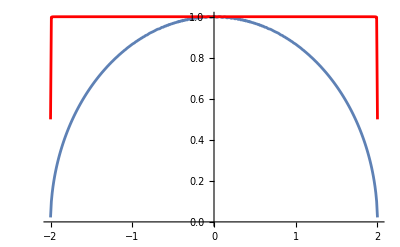

```mathematica
Monitor[Show[ListLinePlot[Table[{ω,-Im[LEFT[ω,0.001,1,0,7000][[1,1]]]},{ω,Range[-2,2,0.01]}]],ListLinePlot[Table[{ω,tr[ω,0.001,1,0]},{ω,Range[-2,2,0.01]}],PlotRange->All,PlotStyle->Red]],ω]
```

```mathematica
list[n0_,n1_,n2_]:=Sort[Join[RandomSample[Range[1,33],n0],RandomSample[Range[67,100],n1],RandomSample[Range[34,67],n2]]]
```

```mathematica
Clear[dist]
```

```mathematica
dist[l_,l2_,s_]:=dist[l,l2,s]=Table[list[l,l2,s],5000]
```

```mathematica
dist[1,1,3][[1]]
```

```mathematica
Clear[hop]
```

```mathematica
hop[t_,d_]:=hop[t,d]=Table[Abs[Table[RandomVariate[NormalDistribution[t,d]],5]],5000]
```

```mathematica
CAvg[ω_,n0_,n1_,n2_,number_]:=Module[{list2=dist[n0,n1,n2][[number]]},T=T1[1];zeros=Table[0,100];listimp =ReplacePart[zeros,Partition[list2,1]->1] ;(*Module[{J=(ω+ⅈ*0.001)IdentityMatrix[1]},J-ϵ*];
*)(*t1=hop[t,dis][[number]][[1]];
t2=hop[t,dis][[number]][[2]];t3=hop[t,dis][[number]][[3]];t4=hop[t,dis][[number]][[4]];t5=hop[t,dis][[number]][[5]];*)
sl1= Module[{J=SL[ω,0.001,1,0]},Do[J=Inverse[IdentityMatrix[1]-Inverse[(ω+ⅈ*0.001-0.5*listimp[[unitcell]])*IdentityMatrix[1]].ConjugateTranspose[T].J.T].Inverse[(ω+ⅈ*0.001-0.5*listimp[[unitcell]])*IdentityMatrix[1]],{unitcell,100}];J];
Il1:=Inverse[IdentityMatrix[1]-sl1.T.SR[ω,0.001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[1]-SR[ω,0.001,1,0].T.sl1.T].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]
```

```mathematica
Table[CAvg[w,2,2,2,1],{w,Range[0,2,0.01]}]
```

{0.946654,0.97163,0.988213,0.995634,0.99727,0.996725,0.995851,0.993831,0.986545,0.969454,0.942515,0.909258,0.872069,0.8332,0.797084,0.765669,0.735528,0.705574,0.681366,0.666925,0.661876,0.669446,0.695806,0.740663,0.799138,0.866858,0.931541,0.97701,0.997516,0.996605,0.983342,0.961519,0.927203,0.869055,0.78813,0.692287,0.599126,0.526864,0.47388,0.448313,0.444344,0.466369,0.517216,0.598448,0.7072,0.809355,0.855033,0.823362,0.755261,0.694997,0.6698,0.679626,0.731183,0.813688,0.900405,0.945109,0.911586,0.827895,0.743432,0.686978,0.66664,0.678988,0.715536,0.761118,0.792632,0.792277,0.764998,0.733444,0.719341,0.735502,0.786531,0.866012,0.946489,0.980676,0.942228,0.858823,0.775817,0.716297,0.680333,0.655905,0.628583,0.590804,0.545342,0.504151,0.482257,0.487317,0.529097,0.624928,0.778526,0.935784,0.932172,0.762364,0.593894,0.494449,0.457524,0.478358,0.568548,0.750695,0.963114,0.91768,0.651663,0.452473,0.350588,0.308764,0.307106,0.343902,0.433882,0.605785,0.847914,0.968145,0.861169,0.735841,0.702492,0.778381,0.938941,0.965494,0.694866,0.441064,0.307245,0.244653,0.219353,0.21814,0.239941,0.294459,0.407395,0.620776,0.901404,0.994725,0.880493,0.776043,0.732622,0.717978,0.696913,0.66555,0.651058,0.682932,0.770665,0.853538,0.786605,0.602474,0.4569,0.384671,0.372737,0.423027,0.56858,0.83867,0.995738,0.840529,0.71908,0.763253,0.920837,0.769263,0.422396,0.253562,0.187316,0.163604,0.163914,0.190862,0.274815,0.464418,0.464027,0.310244,0.255137,0.271083,0.383313,0.742998,0.938758,0.536826,0.388019,0.399398,0.558046,0.886998,0.953287,0.810466,0.86178,0.908252,0.594875,0.397682,0.354101,0.390845,0.454147,0.453363,0.411937,0.372507,0.27767,0.202788,0.179179,0.199356,0.329627,0.550901,0.351675,0.288184,0.295403,0.625484,0.221757,0.156956,0.161504,0.202141,0.269782,0.314453,0.0664018}

```mathematica
Fourier[%161]
```

{9.10972+0. ⅈ,-0.120385+0.898101 ⅈ,-0.137648+0.499229 ⅈ,0.246229+0.462014 ⅈ,-0.245965+0.418934 ⅈ,-0.331422+0.45755 ⅈ,0.363739+0.547156 ⅈ,0.511598+0.138182 ⅈ,0.280784+0.215788 ⅈ,0.00815244+0.263105 ⅈ,-0.929929+0.181911 ⅈ,0.245049+0.432154 ⅈ,-0.141022-0.289462 ⅈ,-0.0946798+0.245855 ⅈ,0.263596+0.247734 ⅈ,-0.0810612+0.40689 ⅈ,0.312423-0.0967971 ⅈ,-0.354627-0.0461326 ⅈ,0.115358+0.221097 ⅈ,0.178103+0.33636 ⅈ,-0.0855887-0.136229 ⅈ,-0.0390542+0.321316 ⅈ,0.414975-0.177818 ⅈ,0.0324214+0.241811 ⅈ,-0.0330528-0.289032 ⅈ,-0.0161897+0.0511193 ⅈ,-0.168378-0.013747 ⅈ,-0.0912835+0.311457 ⅈ,0.145182+0.171174 ⅈ,0.153145-0.0486879 ⅈ,0.0229181-0.0714886 ⅈ,-0.084733+0.0120702 ⅈ,-0.00457995+0.202388 ⅈ,0.116376-0.0535317 ⅈ,-0.0701467+0.0810475 ⅈ,0.157523-0.0309716 ⅈ,-0.104555-0.118554 ⅈ,-0.0697324+0.103028 ⅈ,-0.104391+0.0332823 ⅈ,0.0463584+0.205511 ⅈ,0.096163-0.0386303 ⅈ,-0.00585113-0.0260033 ⅈ,-0.178291-0.00416477 ⅈ,-0.0388979+0.196394 ⅈ,0.0313442+0.0930629 ⅈ,0.0136816+0.113357 ⅈ,0.0225654+0.139433 ⅈ,0.13864+0.0704144 ⅈ,0.0700198+0.0195542 ⅈ,0.0316423-0.0183756 ⅈ,-0.0201348+0.0936458 ⅈ,0.105628+0.0669721 ⅈ,0.0687889+0.000566364 ⅈ,0.0392756+0.0123716 ⅈ,0.0575058+0.0166958 ⅈ,0.0345817-0.017229 ⅈ,0.0268292+0.00179463 ⅈ,0.00757992-0.0285744 ⅈ,-0.0197276+0.013495 ⅈ,-0.00729087+0.00619141 ⅈ,-0.0397924+0.042778 ⅈ,0.00739412+0.0614564 ⅈ,0.0230454+0.0688934 ⅈ,0.0595245+0.0123753 ⅈ,-0.0170107+0.00424401 ⅈ,-0.0160844+0.0391751 ⅈ,-0.0198324+0.0850019 ⅈ,0.0486397+0.10195 ⅈ,0.0811248+0.0539657 ⅈ,0.0634773+0.0146826 ⅈ,0.043987+0.00725616 ⅈ,0.00648657+0.0180481 ⅈ,0.0347375+0.0558719 ⅈ,0.0420733+0.0324464 ⅈ,0.0491163+0.0422482 ⅈ,0.0564937+0.0253301 ⅈ,0.058199+0.0168938 ⅈ,0.0429525+0.00709352 ⅈ,0.0404825+0.0239835 ⅈ,0.0563987+0.0183198 ⅈ,0.0593184+0.00303185 ⅈ,0.0470841-0.0103676 ⅈ,0.0336799-0.00455764 ⅈ,0.0329243+0.000423769 ⅈ,0.0368206-0.00019468 ⅈ,0.0287638-0.0050472 ⅈ,0.0328641-0.000766946 ⅈ,0.0259613-0.015156 ⅈ,0.00907126-0.00883911 ⅈ,-0.00379255+0.00581483 ⅈ,0.00250039+0.0294843 ⅈ,0.0247003+0.0332491 ⅈ,0.0302279+0.020109 ⅈ,0.0229392+0.0245901 ⅈ,0.0270297+0.0298346 ⅈ,0.0332555+0.0371154 ⅈ,0.0467845+0.0354867 ⅈ,0.0540809+0.034747 ⅈ,0.0691348+0.0270171 ⅈ,0.0710373+0.0111107 ⅈ,0.0703504+0.0042194 ⅈ,0.0703504-0.0042194 ⅈ,0.0710373-0.0111107 ⅈ,0.0691348-0.0270171 ⅈ,0.0540809-0.034747 ⅈ,0.0467845-0.0354867 ⅈ,0.0332555-0.0371154 ⅈ,0.0270297-0.0298346 ⅈ,0.0229392-0.0245901 ⅈ,0.0302279-0.020109 ⅈ,0.0247003-0.0332491 ⅈ,0.00250039-0.0294843 ⅈ,-0.00379255-0.00581483 ⅈ,0.00907126+0.00883911 ⅈ,0.0259613+0.015156 ⅈ,0.0328641+0.000766946 ⅈ,0.0287638+0.0050472 ⅈ,0.0368206+0.00019468 ⅈ,0.0329243-0.000423769 ⅈ,0.0336799+0.00455764 ⅈ,0.0470841+0.0103676 ⅈ,0.0593184-0.00303185 ⅈ,0.0563987-0.0183198 ⅈ,0.0404825-0.0239835 ⅈ,0.0429525-0.00709352 ⅈ,0.058199-0.0168938 ⅈ,0.0564937-0.0253301 ⅈ,0.0491163-0.0422482 ⅈ,0.0420733-0.0324464 ⅈ,0.0347375-0.0558719 ⅈ,0.00648657-0.0180481 ⅈ,0.043987-0.00725616 ⅈ,0.0634773-0.0146826 ⅈ,0.0811248-0.0539657 ⅈ,0.0486397-0.10195 ⅈ,-0.0198324-0.0850019 ⅈ,-0.0160844-0.0391751 ⅈ,-0.0170107-0.00424401 ⅈ,0.0595245-0.0123753 ⅈ,0.0230454-0.0688934 ⅈ,0.00739412-0.0614564 ⅈ,-0.0397924-0.042778 ⅈ,-0.00729087-0.00619141 ⅈ,-0.0197276-0.013495 ⅈ,0.00757992+0.0285744 ⅈ,0.0268292-0.00179463 ⅈ,0.0345817+0.017229 ⅈ,0.0575058-0.0166958 ⅈ,0.0392756-0.0123716 ⅈ,0.0687889-0.000566364 ⅈ,0.105628-0.0669721 ⅈ,-0.0201348-0.0936458 ⅈ,0.0316423+0.0183756 ⅈ,0.0700198-0.0195542 ⅈ,0.13864-0.0704144 ⅈ,0.0225654-0.139433 ⅈ,0.0136816-0.113357 ⅈ,0.0313442-0.0930629 ⅈ,-0.0388979-0.196394 ⅈ,-0.178291+0.00416477 ⅈ,-0.00585113+0.0260033 ⅈ,0.096163+0.0386303 ⅈ,0.0463584-0.205511 ⅈ,-0.104391-0.0332823 ⅈ,-0.0697324-0.103028 ⅈ,-0.104555+0.118554 ⅈ,0.157523+0.0309716 ⅈ,-0.0701467-0.0810475 ⅈ,0.116376+0.0535317 ⅈ,-0.00457995-0.202388 ⅈ,-0.084733-0.0120702 ⅈ,0.0229181+0.0714886 ⅈ,0.153145+0.0486879 ⅈ,0.145182-0.171174 ⅈ,-0.0912835-0.311457 ⅈ,-0.168378+0.013747 ⅈ,-0.0161897-0.0511193 ⅈ,-0.0330528+0.289032 ⅈ,0.0324214-0.241811 ⅈ,0.414975+0.177818 ⅈ,-0.0390542-0.321316 ⅈ,-0.0855887+0.136229 ⅈ,0.178103-0.33636 ⅈ,0.115358-0.221097 ⅈ,-0.354627+0.0461326 ⅈ,0.312423+0.0967971 ⅈ,-0.0810612-0.40689 ⅈ,0.263596-0.247734 ⅈ,-0.0946798-0.245855 ⅈ,-0.141022+0.289462 ⅈ,0.245049-0.432154 ⅈ,-0.929929-0.181911 ⅈ,0.00815244-0.263105 ⅈ,0.280784-0.215788 ⅈ,0.511598-0.138182 ⅈ,0.363739-0.547156 ⅈ,-0.331422-0.45755 ⅈ,-0.245965-0.418934 ⅈ,0.246229-0.462014 ⅈ,-0.137648-0.499229 ⅈ,-0.120385-0.898101 ⅈ}

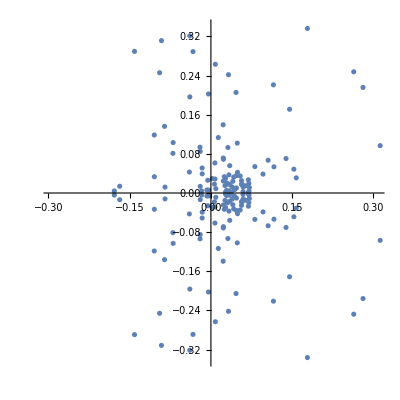

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%162,AspectRatio->1]
```

```mathematica
Table[Monitor[Table[{w,ParallelTable[CAvg[w,2,2,x,number],{number,5000}]//Mean},{w,Range[0,2,0.2]}],{x,w}],{x,0,20,2}]
```

{{{0.,0.760611},{0.2,0.846136},{0.4,0.725457},{0.6,0.617722},{0.8,0.761189},{1.,0.934438},{1.2,0.959421},{1.4,0.798112},{1.6,0.296748},{1.8,0.63836},{2.,0.460787}},{{0.,0.680439},{0.2,0.773767},{0.4,0.670282},{0.6,0.574775},{0.8,0.688899},{1.,0.816158},{1.2,0.817594},{1.4,0.684292},{1.6,0.28509},{1.8,0.469774},{2.,0.0862678}},{{0.,0.625729},{0.2,0.712332},{0.4,0.623817},{0.6,0.523488},{0.8,0.634544},{1.,0.737601},{1.2,0.724618},{1.4,0.600488},{1.6,0.266824},{1.8,0.400404},{2.,0.04887}},{{0.,0.593802},{0.2,0.668365},{0.4,0.577709},{0.6,0.490982},{0.8,0.582494},{1.,0.669778},{1.2,0.653494},{1.4,0.532748},{1.6,0.245223},{1.8,0.335878},{2.,0.0429779}},{{0.,0.552856},{0.2,0.629749},{0.4,0.538766},{0.6,0.471593},{0.8,0.558012},{1.,0.628903},{1.2,0.603807},{1.4,0.498325},{1.6,0.236443},{1.8,0.293734},{2.,0.0455057}},{{0.,0.536181},{0.2,0.609537},{0.4,0.528421},{0.6,0.45371},{0.8,0.532114},{1.,0.594095},{1.2,0.55675},{1.4,0.47119},{1.6,0.235208},{1.8,0.267868},{2.,0.045892}},{{0.,0.514088},{0.2,0.595079},{0.4,0.511266},{0.6,0.439005},{0.8,0.51369},{1.,0.552904},{1.2,0.530249},{1.4,0.441798},{1.6,0.219021},{1.8,0.25406},{2.,0.0543793}},{{0.,0.48723},{0.2,0.577717},{0.4,0.495231},{0.6,0.414781},{0.8,0.488431},{1.,0.529778},{1.2,0.508706},{1.4,0.413204},{1.6,0.20316},{1.8,0.237067},{2.,0.0518017}},{{0.,0.477287},{0.2,0.561112},{0.4,0.471593},{0.6,0.399646},{0.8,0.469272},{1.,0.52059},{1.2,0.488165},{1.4,0.390954},{1.6,0.202386},{1.8,0.235925},{2.,0.0496717}},{{0.,0.467626},{0.2,0.537722},{0.4,0.4564},{0.6,0.385235},{0.8,0.455913},{1.,0.503225},{1.2,0.471549},{1.4,0.383839},{1.6,0.211847},{1.8,0.228866},{2.,0.0515818}},{{0.,0.450653},{0.2,0.537863},{0.4,0.445774},{0.6,0.384832},{0.8,0.459692},{1.,0.496068},{1.2,0.46591},{1.4,0.395711},{1.6,0.202405},{1.8,0.226732},{2.,0.059043}}}

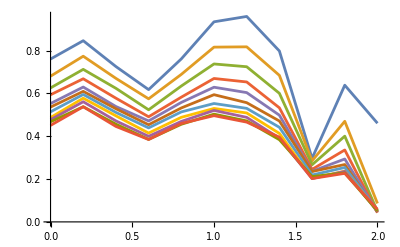

```mathematica
ListPlot[%117,Joined->True]
```

```mathematica
Table[Monitor[Table[{w,ParallelTable[CAvg[w,0,13-x,9,number],{number,5000}]//Mean},{w,Range[0,2,0.2]}],{x,w}],{x,0,10,2}]
```

{{{0.,0.836005},{0.2,0.833074},{0.4,0.829758},{0.6,0.823041},{0.8,0.807418},{1.,0.794574},{1.2,0.775271},{1.4,0.740399},{1.6,0.682436},{1.8,0.595065},{2.,0.37884}},{{0.,0.75665},{0.2,0.75466},{0.4,0.750216},{0.6,0.739952},{0.8,0.729614},{1.,0.709642},{1.2,0.675475},{1.4,0.634071},{1.6,0.567809},{1.8,0.446605},{2.,0.0500333}},{{0.,0.696728},{0.2,0.701561},{0.4,0.692228},{0.6,0.680387},{0.8,0.671297},{1.,0.645769},{1.2,0.612411},{1.4,0.563713},{1.6,0.484354},{1.8,0.359883},{2.,0.038575}},{{0.,0.654002},{0.2,0.661907},{0.4,0.650786},{0.6,0.638472},{0.8,0.618315},{1.,0.596971},{1.2,0.559844},{1.4,0.50828},{1.6,0.433301},{1.8,0.31275},{2.,0.0459692}},{{0.,0.620034},{0.2,0.628884},{0.4,0.618415},{0.6,0.610254},{0.8,0.586231},{1.,0.561136},{1.2,0.527664},{1.4,0.4745},{1.6,0.404266},{1.8,0.290334},{2.,0.0496751}},{{0.,0.591621},{0.2,0.613412},{0.4,0.585154},{0.6,0.572107},{0.8,0.564465},{1.,0.543145},{1.2,0.507031},{1.4,0.448009},{1.6,0.384174},{1.8,0.277638},{2.,0.0509913}}}

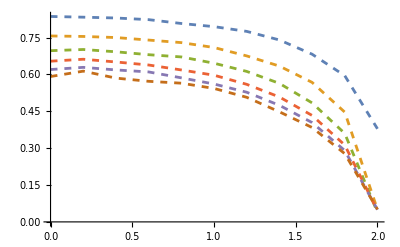

```mathematica
ListPlot[%159,Joined->True,PlotStyle->Dashed]
```

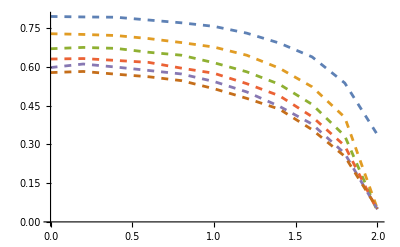

```mathematica
ListPlot[%157,Joined->True,PlotStyle->Dashed]
```

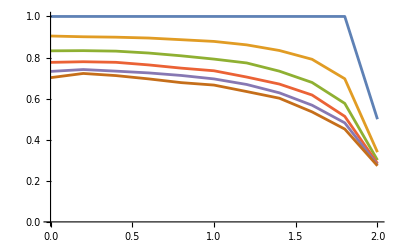

```mathematica
ListPlot[%149,Joined->True]
```

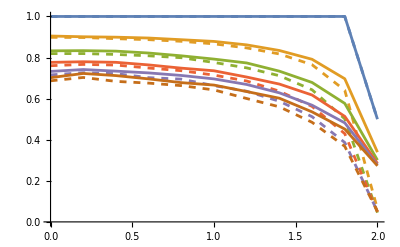

```mathematica
Show[%154,%155]
```

```mathematica
Table[Monitor[Table[{w,ParallelTable[CAvg[w,2,2,x,number],{number,5000}]//Mean},{w,Range[0,2,0.2]}],{x,w}],{x,0,20,2}]
```

{{{0.,0.735409},{0.2,0.829705},{0.4,0.697029},{0.6,0.574844},{0.8,0.732865},{1.,0.92551},{1.2,0.953873},{1.4,0.769204},{1.6,0.170833},{1.8,0.545678},{2.,0.0178282}},{{0.,0.670744},{0.2,0.763404},{0.4,0.64788},{0.6,0.539344},{0.8,0.672951},{1.,0.82907},{1.2,0.832616},{1.4,0.683996},{1.6,0.163537},{1.8,0.459765},{2.,0.0174605}},{{0.,0.646715},{0.2,0.711985},{0.4,0.613249},{0.6,0.501},{0.8,0.62652},{1.,0.761634},{1.2,0.748248},{1.4,0.613293},{1.6,0.155508},{1.8,0.421581},{2.,0.0184553}},{{0.,0.607297},{0.2,0.66887},{0.4,0.58737},{0.6,0.483157},{0.8,0.587117},{1.,0.70328},{1.2,0.684784},{1.4,0.56322},{1.6,0.155457},{1.8,0.390196},{2.,0.0192249}},{{0.,0.574933},{0.2,0.643432},{0.4,0.571209},{0.6,0.465705},{0.8,0.566411},{1.,0.656758},{1.2,0.634601},{1.4,0.544331},{1.6,0.14919},{1.8,0.364307},{2.,0.0197574}},{{0.,0.545817},{0.2,0.621528},{0.4,0.550938},{0.6,0.453112},{0.8,0.549832},{1.,0.623787},{1.2,0.603205},{1.4,0.519567},{1.6,0.142986},{1.8,0.351334},{2.,0.020357}},{{0.,0.521275},{0.2,0.605466},{0.4,0.521699},{0.6,0.43651},{0.8,0.527119},{1.,0.606398},{1.2,0.578469},{1.4,0.495027},{1.6,0.139145},{1.8,0.346416},{2.,0.0204661}},{{0.,0.508056},{0.2,0.586606},{0.4,0.51738},{0.6,0.418292},{0.8,0.505109},{1.,0.588542},{1.2,0.558717},{1.4,0.475373},{1.6,0.142601},{1.8,0.331024},{2.,0.0209638}},{{0.,0.50842},{0.2,0.566461},{0.4,0.494638},{0.6,0.404897},{0.8,0.497707},{1.,0.560557},{1.2,0.542098},{1.4,0.46827},{1.6,0.141664},{1.8,0.329485},{2.,0.0206364}},{{0.,0.49365},{0.2,0.559147},{0.4,0.487551},{0.6,0.399756},{0.8,0.485939},{1.,0.551837},{1.2,0.526676},{1.4,0.472442},{1.6,0.135511},{1.8,0.331539},{2.,0.0209095}},{{0.,0.48265},{0.2,0.547758},{0.4,0.493647},{0.6,0.402545},{0.8,0.491585},{1.,0.541836},{1.2,0.513213},{1.4,0.46253},{1.6,0.135097},{1.8,0.318641},{2.,0.0211008}}}

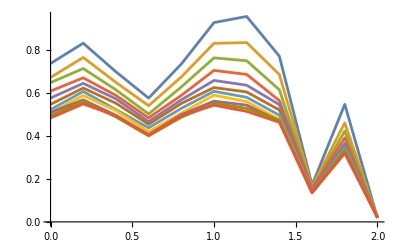

```mathematica
ListPlot[%128,Joined->True]
```

```mathematica
Table[Monitor[Table[{w,ParallelTable[CAvg[w,2,2,x,number],{number,5000}]//Mean},{w,Range[0,2,0.2]}],{x,w}],{x,0,20,2}]
```

{{{0.,0.735409},{0.2,0.829705},{0.4,0.697029},{0.6,0.574844},{0.8,0.732865},{1.,0.92551},{1.2,0.953873},{1.4,0.769204},{1.6,0.170833},{1.8,0.545678},{2.,0.0178282}},{{0.,0.67057},{0.2,0.766625},{0.4,0.652332},{0.6,0.539735},{0.8,0.67501},{1.,0.825381},{1.2,0.831952},{1.4,0.679735},{1.6,0.163073},{1.8,0.456325},{2.,0.0174915}},{{0.,0.644034},{0.2,0.715725},{0.4,0.614094},{0.6,0.504547},{0.8,0.628878},{1.,0.759481},{1.2,0.750662},{1.4,0.612225},{1.6,0.154364},{1.8,0.418406},{2.,0.0184027}},{{0.,0.601104},{0.2,0.671811},{0.4,0.581228},{0.6,0.486006},{0.8,0.59303},{1.,0.705201},{1.2,0.688692},{1.4,0.569025},{1.6,0.152896},{1.8,0.393249},{2.,0.0192593}},{{0.,0.572154},{0.2,0.637799},{0.4,0.567062},{0.6,0.469032},{0.8,0.567927},{1.,0.64918},{1.2,0.631494},{1.4,0.545354},{1.6,0.149679},{1.8,0.372187},{2.,0.019898}},{{0.,0.538748},{0.2,0.622202},{0.4,0.543899},{0.6,0.450516},{0.8,0.548204},{1.,0.626987},{1.2,0.599419},{1.4,0.516094},{1.6,0.142117},{1.8,0.350608},{2.,0.0206104}},{{0.,0.533666},{0.2,0.604674},{0.4,0.529044},{0.6,0.441145},{0.8,0.532263},{1.,0.60284},{1.2,0.573882},{1.4,0.497083},{1.6,0.140044},{1.8,0.341826},{2.,0.0203236}},{{0.,0.511022},{0.2,0.585016},{0.4,0.51409},{0.6,0.418391},{0.8,0.509374},{1.,0.5809},{1.2,0.557466},{1.4,0.466687},{1.6,0.141902},{1.8,0.330486},{2.,0.0208894}},{{0.,0.509224},{0.2,0.576045},{0.4,0.491766},{0.6,0.400887},{0.8,0.496853},{1.,0.568273},{1.2,0.5416},{1.4,0.471248},{1.6,0.138458},{1.8,0.334018},{2.,0.0205363}},{{0.,0.496322},{0.2,0.562135},{0.4,0.487374},{0.6,0.404981},{0.8,0.490671},{1.,0.553797},{1.2,0.5302},{1.4,0.474906},{1.6,0.139031},{1.8,0.324293},{2.,0.0210464}},{{0.,0.478714},{0.2,0.550994},{0.4,0.497683},{0.6,0.40562},{0.8,0.49068},{1.,0.536047},{1.2,0.510469},{1.4,0.466362},{1.6,0.130439},{1.8,0.316548},{2.,0.0208661}}}

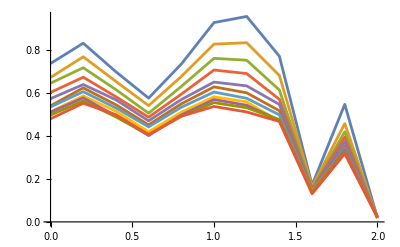

```mathematica
ListPlot[%141,Joined->True]
```

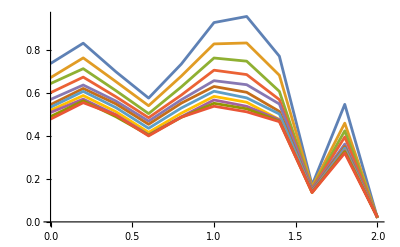

```mathematica
ListPlot[%134,Joined->True]
```

```mathematica
Table[Table[{w,CAvg[w,1,4,16,50,1,20,40,60,90,num]},{w,Range[0,2,0.2]}],{num,10}]
```

```mathematica
input=%94
```

```mathematica
Transpose[input[[1]]][[2]]
```

```mathematica
Dimensions[ca]
```

{11,11,2}

```mathematica
RandomSample[Abs[Transpose[ca[[1]]][[2]]-Transpose[input[[1]]][[2]]],10]
```

{0.224743,0.285216,0.306043,0.434167,0.498166,0.366871,0.140602,0.108588,0.159129,0.443209}

```mathematica
Clear[misfit]
```

```mathematica
misfit[m_]:=Table[Table[Total[RandomSample[Abs[Transpose[ca[[x]]][[2]]-Transpose[input[[y]]][[2]]],m]],{x,11}],{y,10}]
```

```mathematica
misfit[19]
```

```mathematica
Table[ListPlot[Table[Around[Table[misfit[m][[x]][[y]],{x,10}]],{y,10}],Frame->True,PlotRange->All,PlotStyle->RandomColor[m]],{m,11}]
```

```mathematica
Dimensions[%29]
```

{11,6}

```mathematica
Table[Table[%29[[x]][[y]],{x,11}],{y,6}]
```

{{0.558685,0.59944,0.564592,0.550355,0.534972,0.507912,0.476733,0.436772,0.36988,0.276128,0.0548946},{0.516964,0.538897,0.519907,0.50275,0.486705,0.46484,0.429457,0.38119,0.309489,0.227456,0.0545504},{0.507718,0.52194,0.504738,0.495446,0.477745,0.448356,0.414695,0.367322,0.298785,0.218701,0.0535917},{0.515543,0.531056,0.508052,0.499825,0.476935,0.458039,0.419018,0.373255,0.322616,0.241073,0.0433085},{0.537082,0.558025,0.551376,0.527125,0.511801,0.49228,0.460355,0.424289,0.357816,0.291132,0.0469687},{0.599572,0.635729,0.602807,0.600637,0.576959,0.57032,0.533349,0.509317,0.463076,0.422646,0.415516}}

```mathematica
Table[Table[Total[Abs[%41[[x]]-%51[[y]]]],{y,6}],{x,10}]
```

{{3.37353,3.08243,3.00353,3.08315,3.28869,3.84704},{1.85253,1.85141,1.85597,1.86178,1.90914,2.33063},{2.36057,2.3339,2.33831,2.35556,2.29469,2.53397},{2.68325,2.46335,2.41975,2.4389,2.53487,3.27655},{2.20873,1.82173,1.7263,1.80776,2.0679,3.0632},{2.15706,2.11298,2.11144,2.13105,2.07497,2.37308},{1.94889,2.02155,2.04904,2.03239,1.9809,2.50933},{2.1299,2.05208,2.09439,2.13152,2.10264,2.57114},{2.49755,2.41044,2.44092,2.42652,2.49948,2.49285},{1.85958,1.88027,1.92135,1.92538,1.91766,2.40299}}

```mathematica
Show[ListLinePlot[Table[Around[Table[%78[[x]][[y]],{x,10}]],{y,6}],Frame->True,PlotStyle->Black],ListPlot[Table[Mean[Table[%78[[x]][[y]],{x,10}]],{y,6}],PlotStyle->Directive[Red,PointSize[0.02]]]]
```

```mathematica
Table[{num,Mean[Table[Abs[Misfit[1.99,-2,n,num]-num]/num,{n,Range[1,100,1]}]]},{num,1,25}]
```

{{1,0},{2,0},{3,0},{4,0},{5,3/500},{6,1/60},{7,13/700},{8,7/200},{9,7/225},{10,19/500},{11,41/1100},{12,41/1200},{13,27/650},{14,9/200},{15,17/300},{16,19/400},{17,47/850},{18,47/900},{19,109/1900},{20,109/2000},{21,127/2100},{22,53/1100},{23,33/575},{24,113/2400},{25,79/2500}}

```mathematica
curve=BSplineFunction[%70,SplineDegree->3]
```

BSplineFunction[…]

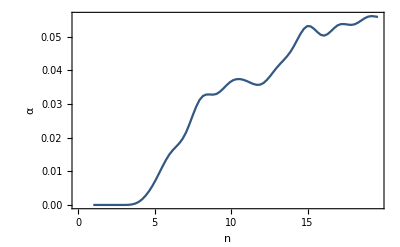

```mathematica
ListLinePlot[Table[curve[x],{x,0,0.8,0.01}],Frame->True,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[α],None},{HoldForm[n],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",12.5,GrayLevel[0]}]
```

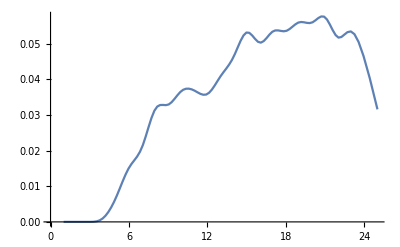

```mathematica
ListPlot[%78,Joined->True]
```

```mathematica
img2= Import["~/Downloads/test1.eps"]
```

```mathematica
hFilter=Closing[img2,BoxMatrix[{10,0}]];
vFilter=Closing[img2,BoxMatrix[{0,10}]];
```

```mathematica
grid=ImageApply[Min,{hFilter,vFilter}]
```

-Graphics-

```mathematica
Clear[img]
```

```mathematica
img=Binarize[ImageDifference[img2,grid]]
```

-Graphics-

```mathematica
pt={ImageDimensions[img2]/4,ImageDimensions[img2]/2};
LocatorPane[Dynamic[pt],Dynamic[Show[img2,Graphics[{EdgeForm[Black],FaceForm[],Rectangle@@pt}]]],Appearance->Graphics[{Red,AbsolutePointSize[5],Point[{0,0}]}]]
```

```mathematica
res=ComponentMeasurements[MorphologicalComponents[ColorNegate[Binarize[ImageCorrelate[img2,ImageTrim[img2,pt],NormalizedSquaredEuclideanDistance],0.18]]],{"Centroid","Area"},#2>1& (*use only the larger hits*)];
```

```mathematica
Show[img,Graphics[{Green,Circle[#,5]&/@res[[All,2,1]]}]]
```

-Graphics-

```mathematica
res
```

{1→{{343.5,78.5},15.5}}

-Graphics-

```mathematica
ResourceFunction["ExtractPlotImageData"][%152]
```

{{1,121/373},{2,122/373},{3,122/373},{4,122/373},{5,122/373},{6,122/373},{7,123/373},{8,123/373},{9,123/373},{10,123/373},{11,124/373},{12,124/373},{13,125/373},{14,126/373},{15,126/373},{16,127/373},{17,126/373},{18,126/373},{19,126/373},{20,128/373},{21,129/373},{22,128/373},{23,128/373},{24,128/373},{25,128/373},{26,128/373},{27,130/373},{28,129/373},{29,129/373},{30,130/373},{31,132/373},{32,132/373},{33,130/373},{34,654/1865},{35,131/373},{36,132/373},{37,131/373},{38,131/373},{39,131/373},{40,132/373},{41,132/373},{42,131/373},{43,131/373},{44,133/373},{45,133/373},{46,134/373},{47,135/373},{48,136/373},{49,137/373},{50,139/373},{51,140/373},{52,418/1119},{53,142/373},{54,144/373},{55,146/373},{56,148/373},{57,150/373},{58,151/373},{59,153/373},{60,154/373},{61,154/373},{62,156/373},{63,155/373},{64,155/373},{65,154/373},{66,154/373},{67,155/373},{68,155/373},{69,155/373},{70,774/1865},{71,470/1119},{72,160/373},{73,161/373},{74,161/373},{75,163/373},{76,164/373},{77,163/373},{78,165/373},{79,166/373},{80,167/373},{81,169/373},{82,169/373},{83,170/373},{84,171/373},{85,172/373},{86,172/373},{87,173/373},{88,174/373},{89,175/373},{90,175/373},{91,175/373},{92,177/373},{93,177/373},{94,178/373},{95,179/373},{96,179/373},{97,179/373},{98,180/373},{99,181/373},{100,181/373},{101,181/373},{102,181/373},{103,181/373},{104,181/373},{105,181/373},{106,181/373},{107,180/373},{108,178/373},{109,176/373},{110,174/373},{111,173/373},{112,171/373},{113,170/373},{114,169/373},{115,167/373},{116,167/373},{117,168/373},{118,169/373},{119,169/373},{120,171/373},{121,171/373},{122,171/373},{123,173/373},{124,173/373},{125,173/373},{126,175/373},{127,175/373},{128,175/373},{129,177/373},{130,177/373},{131,177/373},{132,178/373},{133,179/373},{134,179/373},{135,179/373},{136,179/373},{137,179/373},{138,180/373},{139,181/373},{140,181/373},{141,181/373},{142,181/373},{143,181/373},{144,182/373},{145,182/373},{146,182/373},{147,182/373},{148,183/373},{149,183/373},{150,184/373},{151,184/373},{152,185/373},{153,185/373},{154,187/373},{155,187/373},{156,187/373},{157,187/373},{158,187/373},{159,187/373},{160,187/373},{161,187/373},{162,189/373},{163,191/373},{164,193/373},{165,193/373},{166,193/373},{167,194/373},{168,194/373},{169,195/373},{170,195/373},{171,195/373},{172,197/373},{173,197/373},{174,199/373},{175,199/373},{176,200/373},{177,201/373},{178,202/373},{179,202/373},{180,203/373},{181,204/373},{182,204/373},{183,204/373},{184,205/373},{185,206/373},{186,206/373},{187,206/373},{188,207/373},{189,207/373},{190,207/373},{191,209/373},{192,209/373},{193,209/373},{194,209/373},{195,211/373},{196,211/373},{197,211/373},{198,213/373},{199,213/373},{200,215/373},{201,215/373},{202,215/373},{203,217/373},{204,217/373},{205,218/373},{206,219/373},{207,219/373},{208,221/373},{209,222/373},{210,223/373},{211,224/373},{212,225/373},{213,226/373},{214,228/373},{215,229/373},{216,231/373},{217,231/373},{218,232/373},{219,232/373},{220,232/373},{221,233/373},{222,234/373},{223,236/373},{224,237/373},{225,238/373},{226,239/373},{227,240/373},{228,239/373},{229,237/373},{230,237/373},{231,238/373},{232,240/373},{233,241/373},{234,241/373},{235,242/373},{236,242/373},{237,244/373},{238,245/373},{239,245/373},{240,1756/2611},{241,253/373},{242,254/373},{243,255/373},{244,257/373},{245,260/373},{246,266/373},{247,269/373},{248,272/373},{249,277/373},{250,280/373},{251,282/373},{252,285/373},{253,287/373},{254,290/373},{255,292/373},{256,294/373},{257,298/373},{258,300/373},{259,302/373},{260,304/373},{261,306/373},{262,307/373},{263,307/373},{264,307/373},{265,307/373},{266,307/373},{267,307/373},{268,306/373},{269,305/373},{270,303/373},{271,302/373},{272,300/373},{273,298/373},{274,296/373},{275,294/373},{276,292/373},{277,289/373},{278,287/373},{279,283/373},{280,279/373},{281,273/373},{282,266/373},{283,255/373},{284,247/373},{285,238/373},{286,235/373},{287,235/373},{288,234/373},{289,233/373},{290,233/373},{291,231/373},{292,231/373},{293,229/373},{294,229/373},{295,227/373},{296,227/373},{297,225/373},{298,225/373},{299,223/373},{300,222/373},{301,221/373},{302,220/373},{303,219/373},{304,218/373},{305,217/373},{306,217/373},{307,215/373},{308,215/373},{309,214/373},{310,212/373},{311,211/373},{312,210/373},{313,209/373},{314,207/373},{315,207/373},{316,205/373},{317,205/373},{318,204/373},{319,203/373},{320,203/373},{321,202/373},{322,200/373},{323,196/373},{324,195/373},{325,194/373},{326,194/373},{327,194/373},{328,195/373},{329,196/373},{330,196/373},{331,198/373},{332,199/373},{333,200/373},{334,201/373},{335,204/373},{336,208/373},{337,212/373},{338,217/373},{339,223/373},{340,228/373},{341,233/373},{342,239/373},{343,244/373},{344,250/373},{345,255/373},{346,260/373},{347,265/373},{348,269/373},{349,273/373},{350,277/373},{351,280/373},{352,284/373},{353,288/373},{354,292/373},{355,297/373},{356,301/373},{357,305/373},{358,307/373},{359,310/373},{360,311/373},{361,313/373},{362,314/373},{363,317/373},{364,319/373},{365,321/373},{366,321/373},{367,323/373},{368,323/373},{369,323/373},{370,323/373},{371,323/373},{372,323/373},{373,322/373},{374,321/373},{375,321/373},{376,319/373},{377,319/373},{378,317/373},{379,317/373},{380,315/373},{381,315/373},{382,313/373},{383,313/373},{384,313/373},{385,312/373},{386,314/373},{387,319/373},{388,321/373},{389,324/373},{390,327/373},{391,330/373},{392,333/373},{393,335/373},{394,338/373},{395,340/373},{396,342/373},{397,344/373},{398,346/373},{399,347/373},{400,349/373},{401,354/373},{402,1066/1119},{403,351/373},{404,351/373},{405,356/373},{406,358/373},{407,362/373},{408,364/373},{409,364/373},{410,364/373},{411,364/373},{412,364/373},{413,364/373},{414,364/373},{415,364/373},{416,364/373},{417,364/373},{418,364/373},{419,364/373},{420,364/373},{421,365/373},{422,366/373},{423,366/373},{424,367/373},{425,369/373},{426,369/373},{427,371/373},{428,371/373},{429,371/373},{430,371/373},{431,371/373},{432,372/373},{433,372/373},{434,1},{435,1},{436,1},{437,1},{438,1},{439,1},{440,1},{441,1},{442,372/373},{443,371/373},{444,370/373},{445,369/373},{446,369/373},{447,369/373},{448,368/373},{449,368/373},{450,368/373},{451,369/373},{452,5940/6341},{453,348/373},{454,701/746},{455,329/373},{456,329/373},{457,327/373},{458,327/373},{459,325/373},{460,325/373},{461,325/373},{462,323/373},{463,322/373},{464,322/373},{465,320/373},{466,319/373},{467,319/373},{468,318/373},{469,317/373},{470,316/373},{471,315/373},{472,313/373},{473,313/373},{474,311/373},{475,311/373},{476,309/373},{477,309/373},{478,307/373},{479,307/373},{480,305/373},{481,305/373},{482,304/373},{483,303/373},{484,303/373},{485,301/373},{486,301/373},{487,300/373},{488,299/373},{489,299/373},{490,299/373},{491,299/373},{492,298/373},{493,297/373},{494,297/373},{495,297/373},{496,297/373},{497,295/373},{498,295/373},{499,294/373},{500,293/373},{501,292/373},{502,291/373},{503,290/373},{504,289/373},{505,288/373},{506,287/373},{507,286/373},{508,285/373},{509,283/373},{510,283/373},{511,281/373},{512,281/373},{513,279/373},{514,278/373},{515,276/373},{516,275/373},{517,273/373},{518,273/373},{519,272/373},{520,270/373},{521,269/373},{522,269/373},{523,269/373},{524,270/373},{525,271/373},{526,273/373},{527,274/373},{528,275/373},{529,276/373},{530,276/373},{531,277/373},{532,278/373},{533,279/373},{534,279/373},{535,279/373},{536,279/373},{537,281/373},{538,282/373},{539,284/373},{540,286/373},{541,289/373},{542,292/373},{543,294/373},{544,299/373},{545,302/373},{546,307/373},{547,311/373},{548,314/373},{549,315/373},{550,317/373},{551,318/373},{552,320/373},{553,321/373},{554,322/373},{555,323/373},{556,324/373},{557,325/373},{558,326/373},{559,327/373},{560,327/373},{561,329/373},{562,329/373},{563,329/373},{564,331/373},{565,331/373},{566,331/373},{567,333/373},{568,333/373},{569,333/373},{570,333/373},{571,334/373},{572,335/373},{573,335/373},{574,335/373},{575,335/373},{576,337/373},{577,337/373},{578,337/373},{579,337/373},{580,337/373},{581,337/373},{582,339/373},{583,339/373},{584,339/373},{585,339/373},{586,339/373},{587,341/373},{588,341/373},{589,341/373},{590,343/373},{591,343/373},{592,343/373},{593,345/373},{594,345/373},{595,345/373},{596,345/373},{597,345/373},{598,343/373},{599,343/373},{600,342/373},{601,341/373},{602,340/373},{603,338/373},{604,337/373},{605,336/373},{606,336/373},{607,337/373},{608,337/373},{609,337/373},{610,337/373},{611,337/373},{612,337/373},{613,335/373},{614,335/373},{615,335/373},{616,333/373},{617,332/373},{618,331/373},{619,330/373},{620,329/373},{621,328/373},{622,327/373},{623,326/373},{624,325/373},{625,324/373},{626,323/373},{627,321/373},{628,321/373},{629,318/373},{630,317/373},{631,316/373},{632,317/373},{633,316/373},{634,315/373},{635,313/373},{636,313/373},{637,312/373},{638,312/373},{639,309/373},{640,309/373},{641,307/373},{642,304/373},{643,303/373},{644,302/373},{645,301/373},{646,301/373},{647,301/373},{648,299/373},{649,297/373},{650,295/373},{651,294/373},{652,292/373},{653,290/373},{654,285/373},{655,281/373},{656,278/373},{657,271/373},{658,266/373},{659,262/373},{660,260/373},{661,256/373},{662,253/373},{663,246/373},{664,237/373},{665,233/373},{666,228/373},{667,889/1492},{668,210/373},{669,3764/7087},{670,911/1865},{671,687/1492},{672,655/1492},{673,152/373},{674,150/373},{675,149/373},{676,147/373},{677,146/373},{678,144/373},{679,142/373},{680,140/373},{681,139/373},{682,137/373},{683,135/373},{684,134/373},{685,132/373},{686,131/373},{687,130/373},{688,129/373},{689,128/373},{690,127/373},{691,127/373},{692,125/373},{693,125/373},{694,123/373},{695,123/373},{696,123/373},{697,121/373},{698,120/373},{699,119/373},{700,119/373},{701,119/373},{702,119/373},{703,119/373},{704,119/373},{705,119/373},{706,119/373},{707,119/373},{708,119/373},{709,119/373},{710,119/373},{711,119/373},{712,119/373},{713,119/373},{714,118/373},{715,117/373},{716,117/373},{717,117/373},{718,117/373},{719,117/373},{720,117/373},{721,117/373},{722,115/373},{723,114/373},{724,113/373},{725,114/373},{726,114/373},{727,114/373},{728,338/1119},{729,111/373},{730,109/373},{731,109/373},{732,108/373},{733,107/373},{734,106/373},{735,105/373},{736,104/373},{737,103/373},{738,102/373},{739,101/373},{740,101/373},{741,99/373},{742,99/373},{743,98/373},{744,97/373},{745,95/373},{746,95/373},{747,93/373},{748,93/373},{749,91/373},{750,91/373},{751,91/373},{752,89/373},{753,87/373},{754,87/373},{755,86/373},{756,85/373},{757,84/373},{758,83/373},{759,84/373},{760,83/373},{761,81/373},{762,80/373},{763,80/373},{764,78/373},{765,77/373},{766,77/373},{767,77/373},{768,76/373},{769,73/373},{770,73/373},{771,72/373},{772,73/373},{773,72/373},{774,70/373},{775,480/2611},{776,67/373},{777,67/373},{778,67/373},{779,66/373},{780,66/373},{781,64/373},{782,64/373},{783,64/373},{784,64/373},{785,63/373},{786,63/373},{787,61/373},{788,59/373},{789,57/373},{790,56/373},{791,55/373},{792,55/373},{793,55/373},{794,53/373},{795,53/373},{796,53/373},{797,52/373},{798,53/373},{799,52/373},{800,51/373},{801,50/373},{802,48/373},{803,46/373},{804,45/373},{805,45/373},{806,44/373},{807,43/373},{808,42/373},{809,41/373},{810,39/373},{811,39/373},{812,39/373},{813,38/373},{814,37/373},{815,37/373},{816,37/373},{817,35/373},{818,35/373},{819,35/373},{820,34/373},{821,33/373},{822,33/373},{823,31/373},{824,31/373},{825,30/373},{826,29/373},{827,29/373},{828,29/373},{829,28/373},{830,28/373},{831,28/373},{832,28/373},{833,28/373},{834,26/373},{835,26/373},{836,25/373},{837,25/373},{838,25/373},{839,24/373},{840,23/373},{841,23/373},{842,22/373},{843,20/373},{844,62/1119},{845,19/373},{846,20/373},{847,20/373},{848,62/1119},{849,15/373},{850,15/373},{851,15/373},{852,16/373},{853,14/373},{854,15/373},{855,14/373},{856,14/373},{857,12/373},{858,10/373},{859,10/373},{860,10/373},{861,9/373},{862,8/373},{863,7/373},{864,7/373},{865,6/373},{866,5/373},{867,5/373},{868,3/373},{869,3/373},{870,4/373},{871,3/373},{872,2/373},{873,2/373},{874,2/373},{875,3/373},{876,3/373}}

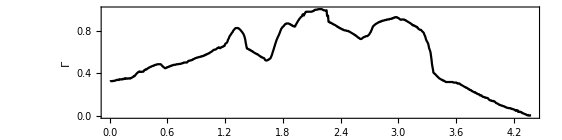

```mathematica
ListPlot[Transpose[Join[{N[Transpose[%156][[1]]/200]},{Transpose[%156][[2]]}]],Joined->True,Frame->True,AspectRatio->1/4,PlotStyle->Black,FrameLabel->{{HoldForm[Γ],None},{HoldForm[ω],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0.1]}]
```

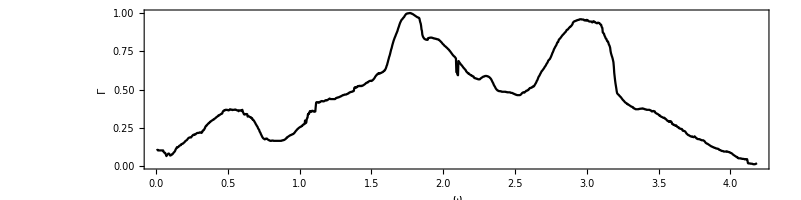

```mathematica
Show[ListPlot[Transpose[Join[{N[Transpose[%48][[1]]/350]},{Transpose[%48][[2]]}]],Joined->True,Frame->True,AspectRatio->1/4,PlotStyle->Black],FrameLabel->{{HoldForm[Γ],None},{HoldForm[ω],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0.1]}]
```

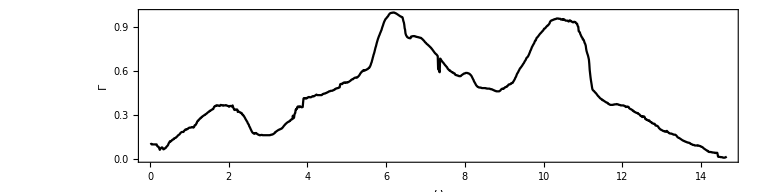

```mathematica
Show[%68,PlotLabel->None,LabelStyle->{FontFamily->"Ubuntu",GrayLevel[0]}]
```

```mathematica
Export["~/newmaterial/mauro_rio_2.pdf",%158]
```

~/newmaterial/mauro_rio_2.pdf

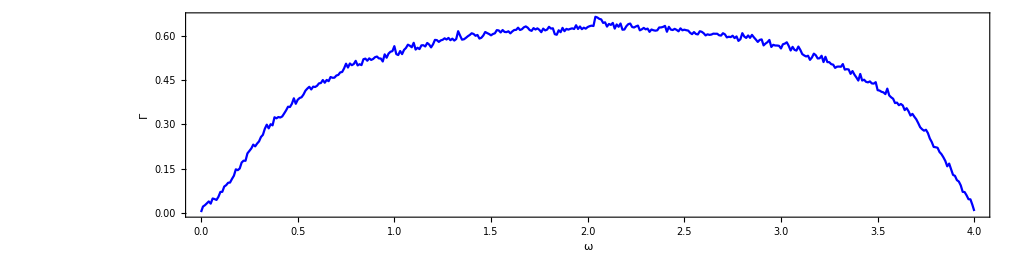

```mathematica
ListLinePlot[Transpose[Join[{Transpose[transmission[10]][[1]]+2},{Transpose[transmission[10]][[2]]}]],AspectRatio->1/4,Frame->True,PlotStyle->Blue,FrameLabel->{{HoldForm[Γ],None},{HoldForm[ω],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0.1]}]
```

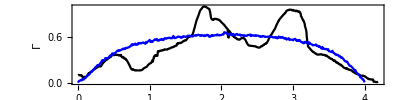

```mathematica
Show[%125,%133]
```

```mathematica
Export["~/newmaterial/mauro_rio_trans_conc.pdf",%138]
```

~/newmaterial/mauro_rio_trans_conc.pdf